# Wave Packet Statistics

Here we’ll answer the question “What are the position and momentum of my particle, and how well do I know them?”.

## The wave packet amplitude function Ψ(x)

We start with the same wave function we had last week; a wave packet centered at x_0 with width d and wave-number k_0.

```mathematica
$Assumptions={d>0,ℏ>0,Element[{x0,k0,d,ℏ},Reals]}
```

{d>0,ℏ>0,(x0|k0|d|ℏ)∈Reals}

```mathematica
Ψ=A Exp[-(x-x0)^2/(2 d^2)]Exp[I k0 (x-x0)]/.A->1/(√d π^(1/4))
```

(ⅇ^(ⅈ k0 (x-x0)-(x-x0)^2/(2 d^2)))/(√d π^(1/4))

```mathematica
Ψ̃=1/Sqrt[2π]Integrate[Ψ Exp[-I k x],{ x,-Infinity,Infinity}]
```

(√d ⅇ^(-1/2 d^2 (k-k0)^2-ⅈ k x0))/π^(1/4)

## The probability distribution functions (PDFs) for Ψ(x) and Ψ̃(k)

The PDFs of x and k are shown below.

```mathematica
Px=Abs[Ψ]^2;
Pk=Abs[Ψ̃]^2;
Manipulate[GraphicsGrid[{{Plot[Px/.{d->10^logD,x0->Subscript[x, 0],k0->Subscript[k, 0]},{x,-10,10},PlotRange->{0,1},Filling->Axis,ImageSize->Small,PlotLabel->"P(x)"],Plot[Pk/.{d->10^logD,x0->Subscript[x, 0],k0->Subscript[k, 0]},{k,-10,10},PlotRange->{0,1},Filling->Axis,ImageSize->Small,PlotLabel->"P̃(k)"]},
{Plot[{Re[Ψ],Abs[Ψ]}/.{d->10^logD,x0->Subscript[x, 0],k0->Subscript[k, 0]},{x,-10,10},PlotRange->{-1,1},Filling->Axis,ImageSize->Small,PlotLabel->"Ψ(x)",PerformanceGoal->Quality],Plot[{Re[Ψ̃],Abs[Ψ̃]}/.{d->10^logD,x0->Subscript[x, 0],k0->Subscript[k, 0]},{k,-10,10},PlotRange->{-1,1},Filling->Axis,ImageSize->Small,PlotLabel->"Ψ̃(k)",PerformanceGoal->Quality]}}],{{logD,0},-1,2,0.1,Appearance->"Labeled"},{{Subscript[x, 0],2},-10,10,0.5,Appearance->"Labeled"},{{Subscript[k, 0],4},-10,10,0.5,Appearance->"Labeled"}]
```

## Why the width in Ψ̃(k) given only k_0 in Ψ(x)?

Let’s try to make the real part of our wave packet from a finite collection of sine-waves.

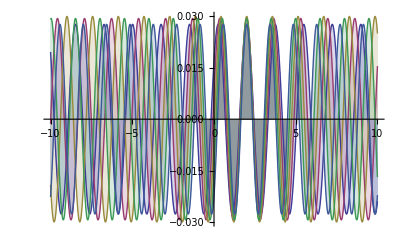

```mathematica
values={d->1,x0->2,k0->4};
dk=d/10;
PsiWave=Re[Ψ̃ Exp[I k x]]dk/Sqrt[2 π]/.{k->(k0+dk#)}/.values&;
waves={PsiWave[-4],PsiWave[-2],PsiWave[0],PsiWave[2],PsiWave[4]};
Plot[waves,{x,-10,10},Filling->Axis,PerformanceGoal->Quality]
```

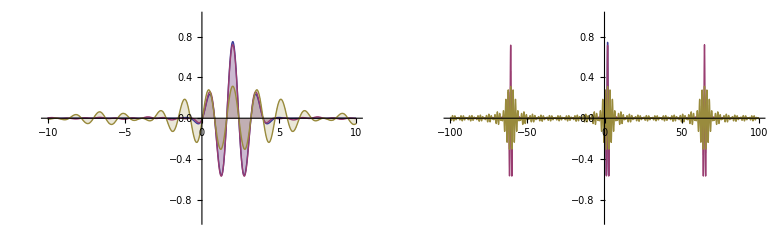

```mathematica
SumPsiWave=Sum[PsiWave[n],{n,-#,#}]&;
waves={Re[Ψ]/.values,SumPsiWave[20],SumPsiWave[5]};
GraphicsRow[{Plot[waves,{x,-10,10},PlotRange->{-1,1},Filling->Axis,ImageSize->Medium],Plot[waves,{x,-100,100},PlotRange->{-1,1},Filling->Axis]}]
```

## The expectation value and uncertainty in x and k

Just what you would expect.

```mathematica
x̄=Integrate[x Px,{x,-Infinity,Infinity}]
```

x0

```mathematica
k̄=Integrate[k Pk,{k,-Infinity,Infinity}]
```

k0

Though you might be a bit uncertain.

```mathematica
Δx=Simplify[Sqrt[Integrate[(x-x̄)^2 Px,{x,-Infinity,Infinity}]]]
```

d/(√2)

```mathematica
Δk=Simplify[Sqrt[Integrate[(k-k̄)^2 Pk,{k,-Infinity,Infinity}]]]
```

1/(√2 d)

Putting this all together we see that Δx = d/√2 and Δk = 1/√2d such that Δx Δk = 1/2, which de Broglie tells us means Δx Δp = ℏ/2.

## The momentum operator p̂

Let’s try out this new trick, the momentum operator p̂=-ⅈ ℏ ∂_x.

```mathematica
pPsi=Simplify[-I ℏ D[Ψ, x]]
```

(ⅇ^(((x-x0) (2 ⅈ d^2 k0-x+x0))/(2 d^2)) (d^2 k0+ⅈ (x-x0)) ℏ)/(d^(5/2) π^(1/4))

Is the wave-packet a momentum eigenstate?

```mathematica
Simplify[pPsi / Ψ]
```

((d^2 k0+ⅈ (x-x0)) ℏ)/d^2

No, since  p̂ Ψ=ℏ(k_0+ⅈ (x-x0)/d^2)Ψ, so the prefactor is not a constant (it is a function of x).  But not to worry, we can still compute <p> and Δp.

```mathematica
p̄=Integrate[Ψ*(-I ℏ D[Ψ, x]),{x,-Infinity,Infinity}]
```

k0 ℏ

```mathematica
OverBar[p2]=Integrate[Ψ*(-I ℏ D[(-I ℏ D[Ψ, x]), x]),{x,-Infinity,Infinity}]
```

1/2 (1/d^2+2 k0^2) ℏ^2

```mathematica
Δp=Simplify[Sqrt[OverBar[p2]-(p̄)^2]]
```

ℏ/(√2 d)

Which is what we expect, since p= ℏ k.